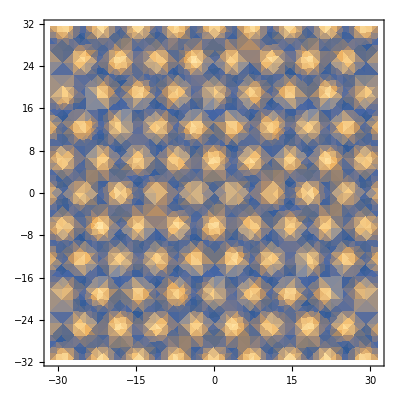

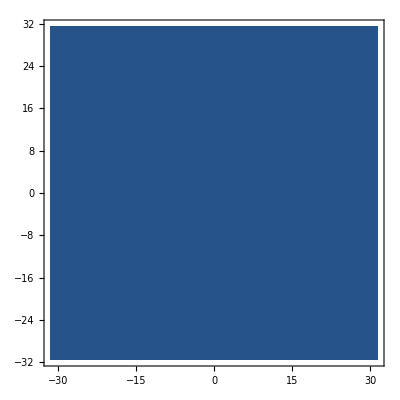

```mathematica
ns[n_,A_,a_,x_,y_]=n+A*(-Cos[(√3 π)/a x]Cos[π/a y]+1/2 Cos[(2π)/a y]);
nl[n_,A_,a_,x_,y_]=n;
DensityPlot[ns[0.0,1.0,2π,x,y],{x,-10π,10π},{y,-10π,10π}]
DensityPlot[nl[0.0,1.0,2π,x,y],{x,-10π,10π},{y,-10π,10π}]
```

计算自由能

```mathematica
fs[n_, ψ_,A_,a_,x_,y_]=ns[n,A,a,x,y]*((L-S)*ns[n,A,a,x,y]+M*ψ^2*ns[n,A,a,x,y]+S*(ns[n,A,a,x,y]+2*Laplacian[ns[n,A,a,x,y],{x,y}]+Laplacian[Laplacian[ns[n,A,a,x,y],{x,y}],{x,y}]))/2-t/3*ns[n,A,a,x,y]^3+v/4*ns[n,A,a,x,y]^4+w/2*ψ^2+u/4*ψ^4;
fl[n_, ψ_,A_,a_,x_,y_]=nl[n,A,a,x,y]*((L-S)*nl[n,A,a,x,y]+M*ψ^2*nl[n,A,a,x,y]+S*(nl[n,A,a,x,y]))/2-t/3*nl[n,A,a,x,y]^3+v/4*nl[n,A,a,x,y]^4+w/2*ψ^2+u/4*ψ^4;

Fs[n_,ψ_,A_,a_]=Integrate[Integrate[fs[n, ψ,A,a,x,y],{x,0,(2 a)/(√3)}],{y,0,2a}]/((4 a^2)/(√3));
Fl[n_,ψ_,A_,a_]=Integrate[Integrate[fl[n, ψ,A,a,x,y],{x,0,1}],{y,0,1}]/(1);
```

求A的表达式

```mathematica
Solve[D[Fs[n,ψ,A,a],A]==0,A]
```

{{A→0},{A→(4 (a^4 t-3 a^4 n v-√(a^8 t^2-15 a^8 L v+120 a^6 π^2 S v-240 a^4 π^4 S v+24 a^8 n t v-36 a^8 n^2 v^2-15 a^8 M v ψ^2)))/(15 a^4 v)},{A→(4 (a^4 t-3 a^4 n v+√(a^8 t^2-15 a^8 L v+120 a^6 π^2 S v-240 a^4 π^4 S v+24 a^8 n t v-36 a^8 n^2 v^2-15 a^8 M v ψ^2)))/(15 a^4 v)}}

```mathematica
As[n_,a_,ψ_]=(4 (a^4 t-3 a^4 n v+√(a^8 t^2-15 a^8 L v+120 a^6 π^2 S v-240 a^4 π^4 S v+24 a^8 n t v-36 a^8 n^2 v^2-15 a^8 M v ψ^2)))/(15 a^4 v);
```

```mathematica
Ftr[n_,ψ_]=Fs[n,ψ,As[n,6.927,ψ],6.927];
Flq[n_,ψ_]=Fl[n,ψ,A,6.927];
```

```mathematica
L=0.7;M=-1.8;S=1.0;t=0.6;v=1.0;w=1.0;u=4.0;
```

```mathematica
Manipulate[Plot[{Ftr[n,ψ],Flq[n,ψ]},{n,-0.3,0.3},
PlotLegends->{"triangle","liquid"}],{ψ,-0.2,0.2}]
```

{-0.1 ； (ns→-0.146202),-0.1 ； (nl→-0.25049)}

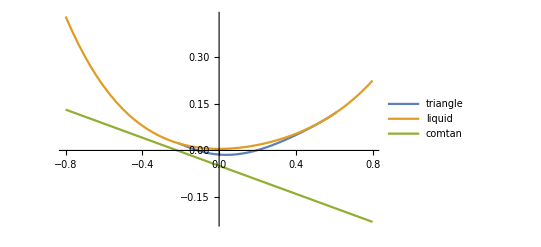

```mathematica
ψ1=-0.1；
comtansol=FindRoot[{D[Flq[nl,ψ1],nl]==D[Ftr[ns,ψ1],ns],D[Ftr[ns,ψ1],ns]==(Ftr[ns,ψ1]-Flq[nl,ψ1])/(ns-nl)},{ns,-0.1},{nl,0.0}]
comtanline[n0_]:=Ftr[ns,ψ1]+D[Flq[nl,ψ1],nl](n0-nl)/.comtansol;
Plot[{Ftr[n0,ψ1],Flq[n0,ψ1],comtanline[n0]},{n0,-.8,.8},PlotLegends->{"triangle","liquid","comtan"}]
```

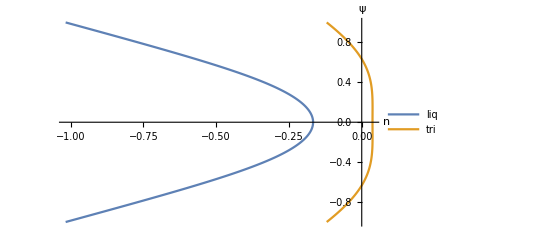

```mathematica
calPhad[ψ_]:={nl, ns}/.Join[FindRoot[{D[Flq[nl,ψ],nlq]==D[Ftr[ns,ψ],ns],D[Flq[nl,ψ],nl]==(Flq[nl,ψ]-Ftr[ns,ψ])/(nl-ns)},{nl,-0.2},{ns,-0.1}]];
data = Transpose[calPhad[#]&/@Range[-1,1,.005]];
epsilon = Range[-1,1,.005];
ListLinePlot[Transpose[{#,epsilon}]&/@data,AxesLabel->{"n","ψ"}, PlotLegends->{"liq","tri"}]
```